```mathematica
numbers={a->1.,ν->0.07453,α->0.000002};
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

F:\Загрузки\Диплом\Diploma_Nb

```mathematica
SetOptions[{Plot,ListPlot,ListLinePlot,ListLogLinearPlot},PlotRange->Full,Axes->False,Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Gray,Dashed],BaseStyle->{FontFamily->"Courier",FontSize->12, Bold},ImageSize->500,PlotStyle->{Red,PointSize[0.01]}];
```

```mathematica
AbsFourier[x_]:=Abs[Take[Fourier[x,FourierParameters->{-1, -1}],{1,Length[x]/2+1}]]
```

```mathematica
NumPlace[x_]:=Position[AbsFourier[x],Max[AbsFourier[x]]][[1,1]]
```

```mathematica
FreqList[x_]:=Table[1.0*b/Length[x],{b,0,Length[x]-1}]
```

```mathematica
Freq[x_]:=FreqList[x][[NumPlace[x]]]
```

```mathematica
TruePlot[x_]:=ListPlot[Transpose[{FreqList[x][[NumPlace[x]-4;;NumPlace[x]+4]],AbsFourier[x][[NumPlace[x]-4;;NumPlace[x]+4]]}],FrameLabel->{"ν","A, mm"}]
FullPlot[x_]:=ListPlot[Transpose[{FreqList[x][[1;;Length[x]/2+1]],AbsFourier[x]}],FrameLabel->{"ν","A, mm"}]
```

0% Level

```mathematica
sig0=Table[a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,128}];
```

0.078125

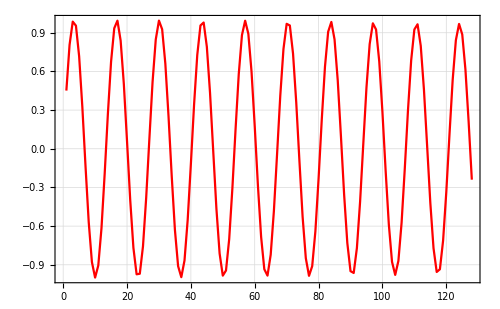

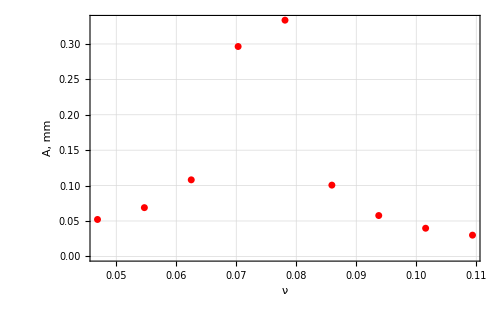

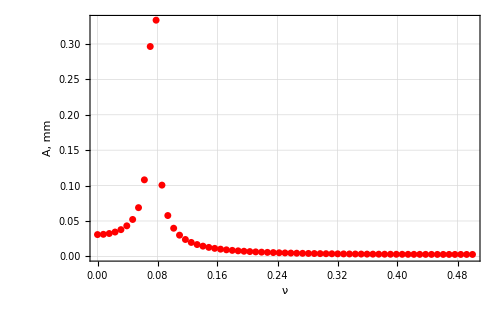

```mathematica
Freq0 =Freq[sig0]
Image0=ListLinePlot[sig0]
Fourier0=TruePlot[sig0]
FourierFull0=FullPlot[sig0]
```

25% Level

```mathematica
sig25=Table[0.5*(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,128}];
```

0.078125

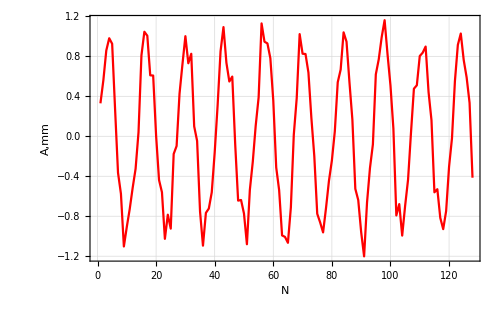

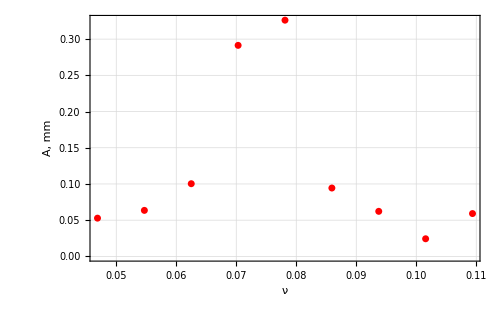

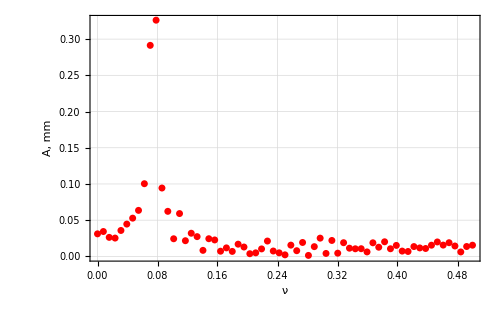

ModelSig.png

```mathematica
Freq25=Freq[sig25]
Image25=ListLinePlot[sig25,FrameLabel->{"N","A,mm"}]
Fourier25=TruePlot[sig25]
FourierFull25=FullPlot[sig25]
Export["ModelSig.png",Image25]
```

50% Level

0.078125

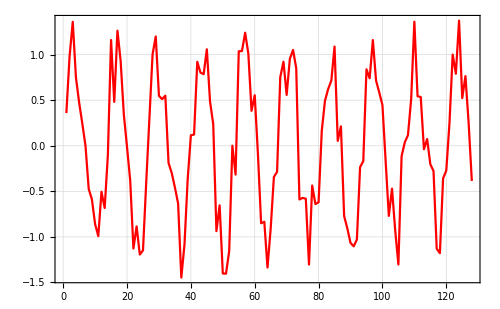

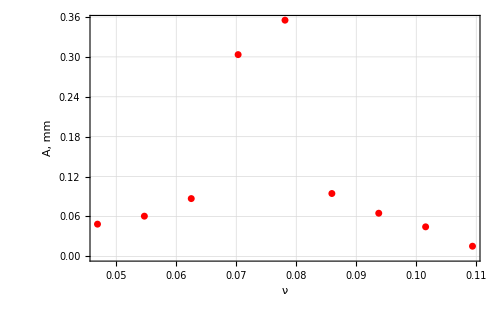

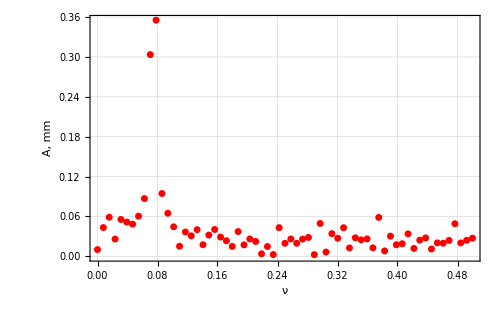

```mathematica
sig50=Table[(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,128}];
Freq50 =Freq[sig50]
Image50=ListLinePlot[sig50]
Fourier50=TruePlot[sig50]
FourierFull50=FullPlot[sig50]
```

75% Level

0.078125

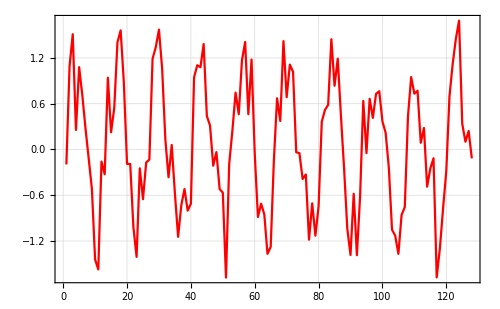

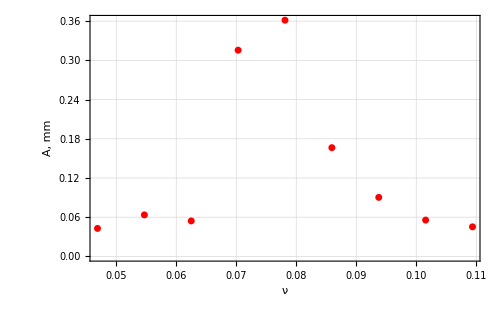

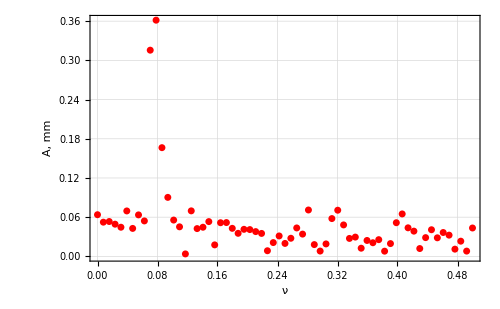

```mathematica
sig75=Table[1.5*(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,128}];
Freq75 =Freq[sig75]
Image75=ListLinePlot[sig75]
Fourier75=TruePlot[sig75]
FourierFull75=FullPlot[sig75]
```

100% Level

0.078125

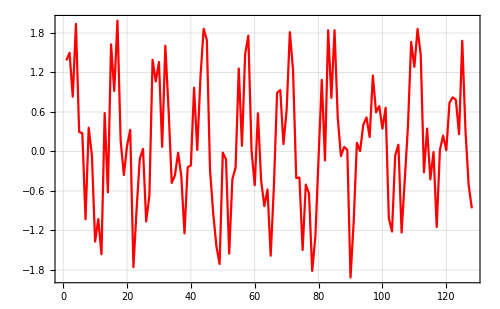

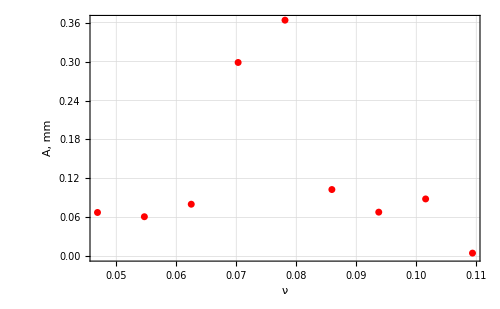

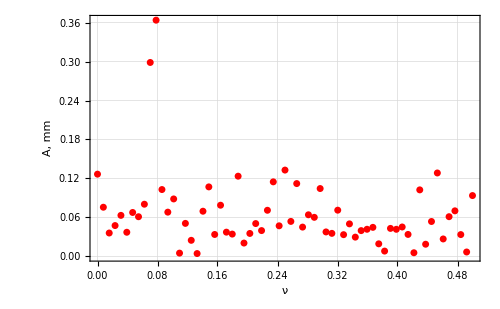

```mathematica
sig100=Table[2*(Random[]-0.5)+a E^(-α k^2)Sin[2 π ν k]/.numbers,{k,1,128}];
Freq100 =Freq[sig100]
Image100=ListLinePlot[sig100]
Fourier100=TruePlot[sig100]
FourierFull100=FullPlot[sig100]
```

```mathematica
depen =Transpose[{{0,25,50,75,100},{Freq0, Freq25,Freq50,Freq75,Freq100}*1000-ν*1000}/.numbers]
```

{{0,3.595},{25,3.595},{50,3.595},{75,3.595},{100,3.595}}

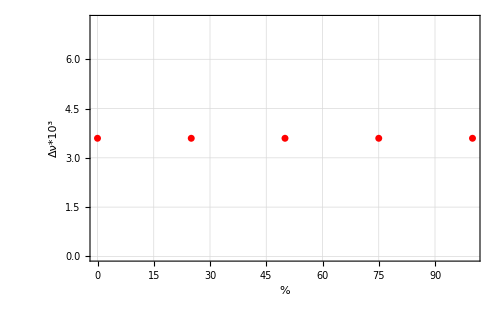

```mathematica
DeltaFourier=ListPlot[depen,Axes->True,FrameLabel->{"%","Δν*10^3"}]
```

```mathematica
Export["DeltaFourierNoise.png",DeltaFourier]
```

DeltaFourierNoise.png